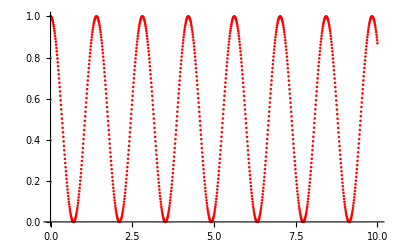

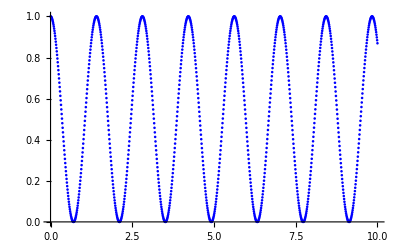

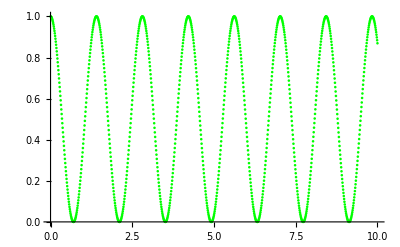

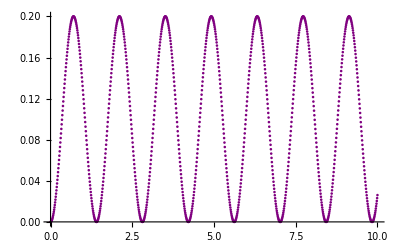

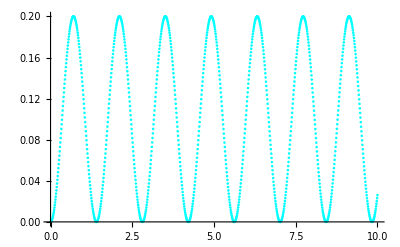

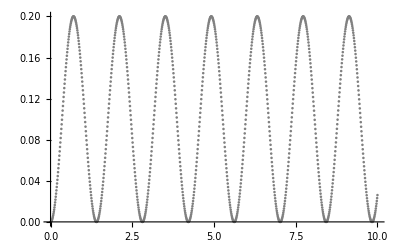

```mathematica
(*Star node network*)
a={{0,1,1,1,1,1},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0}};
(*Choosing node 1 to be excited*)
ρ0={{1},{0},{0},{0},{0},{0}};
state=KroneckerProduct[ρ0,ConjugateTranspose[ρ0]];
(*Defining the evolution of the state*)
ρ1[t_]:=U[t].state.ConjugateTranspose[U[t]]
(*Investigating the probability of the state*)
plot1values=Table[{t,ρ1[t][[1,1]]},{t,0,10,0.01}];
plot1=ListPlot[plot1values,PlotStyle->Red]
plot2values=Table[{t,ρ1[t][[2,2]]//N},{t,0,10,0.01}];
plot2=ListPlot[plot1values,PlotStyle->Blue]
plot3values=Table[{t,ρ1[t][[3,3]]},{t,0,10,0.01}];
plot3=ListPlot[plot1values,PlotStyle->Green]
plot4values=Table[{t,ρ1[t][[4,4]]},{t,0,10,0.01}];
plot4=ListPlot[plot4values,PlotStyle->Purple]
plot5values=Table[{t,ρ1[t][[5,5]]},{t,0,10,0.01}];
plot5=ListPlot[plot5values,PlotStyle->Cyan]
plot6values=Table[{t,ρ1[t][[6,6]]},{t,0,10,0.01}];
plot6=ListPlot[plot6values,PlotStyle->Gray]
```

```mathematica
ρ1[0.5]//MatrixForm//Chop
```

(0.191364 | 0.-0.175922 ⅈ | 0.-0.175922 ⅈ | 0.-0.175922 ⅈ | 0.-0.175922 ⅈ | 0.-0.175922 ⅈ
0.+0.175922 ⅈ | 0.161727 | 0.161727 | 0.161727 | 0.161727 | 0.161727
0.+0.175922 ⅈ | 0.161727 | 0.161727 | 0.161727 | 0.161727 | 0.161727
0.+0.175922 ⅈ | 0.161727 | 0.161727 | 0.161727 | 0.161727 | 0.161727
0.+0.175922 ⅈ | 0.161727 | 0.161727 | 0.161727 | 0.161727 | 0.161727
0.+0.175922 ⅈ | 0.161727 | 0.161727 | 0.161727 | 0.161727 | 0.161727)

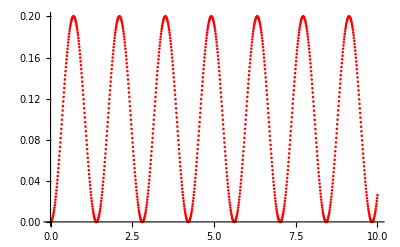

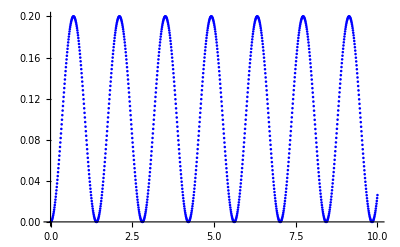

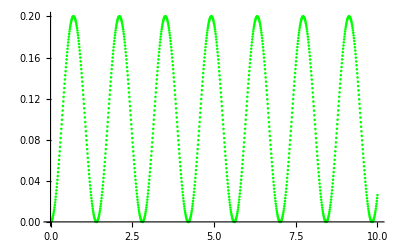

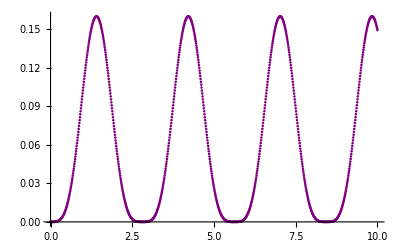

```mathematica
(*Star node network*)
a={{0,1,1,1,1,1},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0}};
(*Choosing node 2 to be excited*)
ρ0={{0},{1},{0},{0},{0},{0}};
state=KroneckerProduct[ρ0,ConjugateTranspose[ρ0]];
(*Defining the evolution of the state*)
ρ1[t_]:=U[t].state.ConjugateTranspose[U[t]]
(*Investigating the probability of the state*)
plot1values=Table[{t,ρ1[t][[1,1]]},{t,0,10,0.01}];
plot1=ListPlot[plot1values,PlotStyle->Red]
plot2values=Table[{t,ρ1[t][[2,2]]//N},{t,0,10,0.01}];
plot2=ListPlot[plot1values,PlotStyle->Blue]
plot3values=Table[{t,ρ1[t][[3,3]]},{t,0,10,0.01}];
plot3=ListPlot[plot1values,PlotStyle->Green]
plot4values=Table[{t,ρ1[t][[4,4]]},{t,0,10,0.01}];
plot4=ListPlot[plot4values,PlotStyle->Purple]
```

```mathematica
(*Star node network*)
a={{0,1,1,1,1,1},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0}};
(*Choosing node 3 to be excited*)
ρ0={{0},{0},{1},{0},{0},{0}};
state=KroneckerProduct[ρ0,ConjugateTranspose[ρ0]];
(*Defining the evolution of the state*)
ρ1[t_]:=U[t].state.ConjugateTranspose[U[t]]
(*Investigating the probability of the state*)
plot1values=Table[{t,ρ1[t][[1,1]]},{t,0,10,0.01}];
plot1=ListPlot[plot1values,PlotStyle->Red]
plot2values=Table[{t,ρ1[t][[2,2]]//N},{t,0,10,0.01}];
plot2=ListPlot[plot1values,PlotStyle->Blue]
plot3values=Table[{t,ρ1[t][[3,3]]},{t,0,10,0.01}];
plot3=ListPlot[plot1values,PlotStyle->Green]
plot4values=Table[{t,ρ1[t][[4,4]]},{t,0,10,0.01}];
plot4=ListPlot[plot4values,PlotStyle->Purple]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

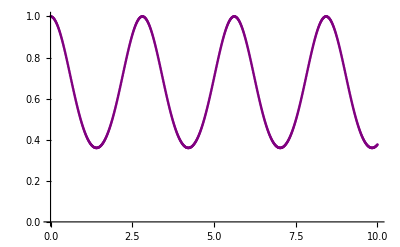

```mathematica
(*Star node network*)
a={{0,1,1,1,1,1},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0}};
(*Choosing node 4 to be excited*)
ρ0={{0},{0},{0},{1},{0},{0}};
state=KroneckerProduct[ρ0,ConjugateTranspose[ρ0]];
(*Defining the evolution of the state*)
ρ1[t_]:=U[t].state.ConjugateTranspose[U[t]]
(*Investigating the probability of the state*)
plot1values=Table[{t,ρ1[t][[1,1]]},{t,0,10,0.01}];
plot1=ListPlot[plot1values,PlotStyle->Red]
plot2values=Table[{t,ρ1[t][[2,2]]//N},{t,0,10,0.01}];
plot2=ListPlot[plot1values,PlotStyle->Blue]
plot3values=Table[{t,ρ1[t][[3,3]]},{t,0,10,0.01}];
plot3=ListPlot[plot1values,PlotStyle->Green]
plot4values=Table[{t,ρ1[t][[4,4]]},{t,0,10,0.01}];
plot4=ListPlot[plot4values,PlotStyle->Purple]
```

```mathematica
(*Star node network*)
a={{0,1,1,1,1,1},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0}};
(*Choosing node 5 to be excited*)
ρ0={{0},{0},{0},{0},{1},{0}};
state=KroneckerProduct[ρ0,ConjugateTranspose[ρ0]];
(*Defining the evolution of the state*)
ρ1[t_]:=U[t].state.ConjugateTranspose[U[t]]
(*Investigating the probability of the state*)
plot1values=Table[{t,ρ1[t][[1,1]]},{t,0,10,0.01}];
plot1=ListPlot[plot1values,PlotStyle->Red]
plot2values=Table[{t,ρ1[t][[2,2]]//N},{t,0,10,0.01}];
plot2=ListPlot[plot1values,PlotStyle->Blue]
plot3values=Table[{t,ρ1[t][[3,3]]},{t,0,10,0.01}];
plot3=ListPlot[plot1values,PlotStyle->Green]
plot4values=Table[{t,ρ1[t][[4,4]]},{t,0,10,0.01}];
plot4=ListPlot[plot4values,PlotStyle->Purple]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*Star node network*)
a={{0,1,1,1,1,1},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0}};
(*Choosing node 6 to be excited*)
ρ0={{0},{0},{0},{0},{0},{1}};
state=KroneckerProduct[ρ0,ConjugateTranspose[ρ0]];
(*Defining the evolution of the state*)
ρ1[t_]:=U[t].state.ConjugateTranspose[U[t]]
(*Investigating the probability of the state*)
plot1values=Table[{t,ρ1[t][[1,1]]},{t,0,10,0.01}];
plot1=ListPlot[plot1values,PlotStyle->Red]
plot2values=Table[{t,ρ1[t][[2,2]]//N},{t,0,10,0.01}];
plot2=ListPlot[plot1values,PlotStyle->Blue]
plot3values=Table[{t,ρ1[t][[3,3]]},{t,0,10,0.01}];
plot3=ListPlot[plot1values,PlotStyle->Green]
plot4values=Table[{t,ρ1[t][[4,4]]},{t,0,10,0.01}];
plot4=ListPlot[plot4values,PlotStyle->Purple]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-